## First example

```mathematica
g = 3/8x^2-3/2x+3/2
```

3/2-(3 x)/2+(3 x^2)/8

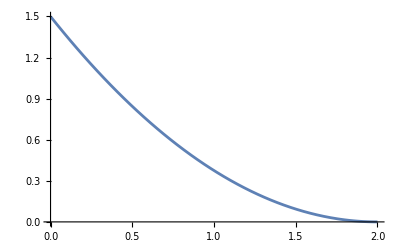

```mathematica
Plot[g,{x,0,2}]
```

```mathematica
A=Integrate[g,{x,0,2}]
k=1/A
```

1

1

```mathematica
f=k*g
F=Integrate[f, {x, 0, x}]
```

3/2-(3 x)/2+(3 x^2)/8

(3 x)/2-(3 x^2)/4+x^3/8

## First example using Piecewise functions

```mathematica
$Assumptions=x∈Reals
g = Piecewise[{{3/8x^2-3/2x+3/2,0<x<2}}]
```

x∈ℝ

Piecewise[{{3/2-(3 x)/2+(3 x^2)/8, 0<x<2}, {0, True}}]

```mathematica
Plot[g,{x,0,2}]
```

-Graphics-

```mathematica
A=Integrate[g,{x,0,2}]
k=1/A
```

1

1

```mathematica
f=k*g
F=Integrate[f, {x, 0, x}]
```

Piecewise[{{3/2-(3 x)/2+(3 x^2)/8, 0<x<2}, {0, True}}]

Piecewise[{{1, x>2}, {1/8 (12 x-6 x^2+x^3), 0<x≤2}, {0, True}}]

## Second example

```mathematica
$Assumptions={lambda >0}
g = Exp[-lambda x]
```

{lambda>0}

ⅇ^(-lambda x)

```mathematica
Manipulate[
Plot[ Exp[-lambda x],{x,0,2},PlotRange->{-1,2}],
{lambda,1,10}
]
```

```mathematica
A=Integrate[g,{x,0,Infinity}]
k=1/A
```

1/lambda

lambda

```mathematica
f=k*g;
F=Integrate[f, {x, 0, x}]
```

1-ⅇ^(-lambda x)

```mathematica
Manipulate[
Plot[ 1-ⅇ^(-lambda x),{x,0,2},PlotRange->{-1,2}],
{lambda,1,10}
]
```

## Third example (#1 in next activity)

```mathematica
f = 1/5
```

1/5

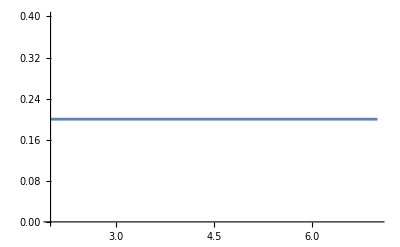

```mathematica
Plot[f,{x,2,7}]
```

```mathematica
Prob=Integrate[f,{x,3,5}]
```

2/5

```mathematica
F=Integrate[f, {x, 2, x}]
```

1/5 (-2+x)

## Fourth example (#2 in next activity)

```mathematica
f = 2x/25
```

(2 x)/25

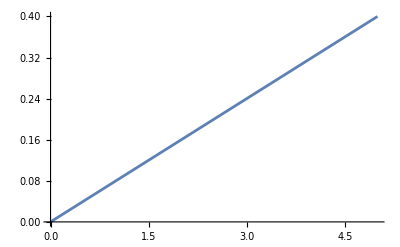

```mathematica
Plot[f,{x,0,5}]
```

```mathematica
Prob=Integrate[f,{x,1,3}]
```

8/25

```mathematica
F=Integrate[f, {x, 0, x}]
```

x^2/25

```mathematica
Integrate[2x/9,{x,0,x}]
```

x^2/9

```mathematica
Integrate[2x/9,{x,1,2}]
```

1/3

```mathematica
Integrate[3x^2/64,{x,1,3}]
```

13/32